```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\MF_DR

```mathematica
sigma0=Import["./sigma0.dat"];
```

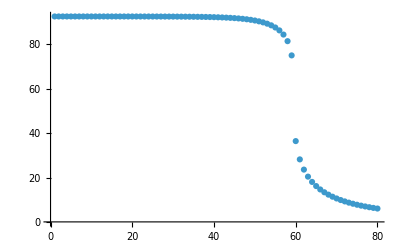

```mathematica
ListPlot[Transpose[sigma0][[30]]]
```

```mathematica
Transpose[sigma0][[30]][[80]]
```

6.01997

```mathematica
mu=Table[i*5.,{i,1,80}];
```

```mathematica
Export["./sigma_mu_T100.dat",Transpose[sigma0][[100]]];
Export["./mu1.dat",mu];
```